```mathematica
ClearAll[ksinglet,ktrap,ktrapdecay,ksinglet,ktriplet1,ktriplet2,kquantumdot];

sol=ParametricNDSolveValue[{
D[singlets[t],t]==-ksinglet*singlets[t]-ktrap*singlets[t],
singlets[t0] == isinglets,

D[trap[t],t]==ktrap*singlets[t]-(ktrapdecay)*trap[t],
trap[t0] == itrap,

D[triplet1[t],t]==2*ksinglet*singlets[t]-(ktriplet1)*triplet1[t]-(ktta*triplet1[t])^2,
triplet1[t0] == itriplet1,

D[tta[t],t]==(ktta*triplet1[t])^2,
tta[t0] == itta,

D[triplet2[t],t]==ktriplet1*triplet1[t]-(ktriplet2)*triplet2[t],
triplet2[t0] == itriplet2,

D[quantumdot[t],t]==ktriplet2*triplet2[t]-(kquantumdot)*quantumdot[t],
quantumdot[t0] == iquantumdot, 

D[photonsoutput[t],t]==(kquantumdot)*quantumdot[t],
photonsoutput[t0] == iphotonsoutput
},
{singlets,trap,triplet1,triplet2,quantumdot,photonsoutput,tta},{t,t0,t1},{ksinglet,ktrap,ktrapdecay,ktriplet1,ktriplet2,kquantumdot,ktta}]
```

ParametricFunction[<>]

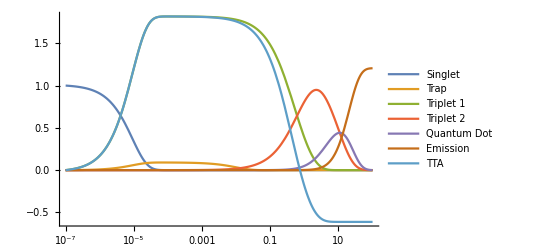

```mathematica
{isinglets,itrap,itriplet1,itriplet2,iquantumdot,iphotonsoutput,itta} = {1,0,0,0,0,0,0}; 
t0= 1*10^(-7);
t1 = 100;
solutions = sol[10^(5) (*ksinglet*),10^4(*ktrap*),10^2 (*ktrapdecay*),1(*ktriplet1*),0.1(*ktriplet2*),0.1(*kquantumdot*),0.8(*tta*)];
ticklabels = {"100 fs", "1 ps", "10 ps", "100 ps", "1 ns", "10 ns", "100 ns", "1 us", "10 us", "100 us"};
LogLinearPlot[{solutions[[1]][t],solutions[[2]][t],solutions[[3]][t],solutions[[4]][t],solutions[[5]][t],solutions[[6]][t],solutions[[3]][t]-solutions[[7]][t]},{t,t0,t1},PlotRange->All,FrameLabel->{{"Population Normalised",""},{"Time [us]",""}},PlotLegends->{"Singlet","Trap","Triplet 1","Triplet 2","Quantum Dot","Emission","TTA"}]
```

```mathematica
photonsoutput
```

```mathematica
SetDirectory[NotebookDirectory[]]
```

/Users/tomikbaikie/Dropbox (Cambridge University)/Physics/Cambridge_Projects_To_Complete/LSC_Singlet_Fission/Figures/SF_Decay_rates

```mathematica
logspace[a_,b_,n_]:=10.0^Range[a,b,(b-a)/(n-1)]
times =logspace[-8,2,1000];
toexport=Table[{t, solutions[[1]][t],solutions[[2]][t],solutions[[3]][t],solutions[[4]][t],solutions[[5]][t],solutions[[6]][t],solutions[[3]][t]-solutions[[7]][t]},{t,times}];
SetDirectory[NotebookDirectory[]];
Export["populations.csv",N[toexport,5]]
```

populations.csv